## Error Bars

```mathematica
Needs["ErrorBarPlots`"]
```

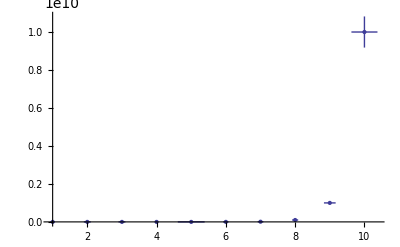

```mathematica
c=Table[{{i,10^i},ErrorBar[RandomReal[i/10],RandomReal[10^i/10]]},{i,1,10}];
errorplot=ErrorListPlot[c,PlotRange->All]
```

```mathematica
lerrorplot=errorplot/.{x_Real,y_Real}->{Log[E,x],Log[E,y]};
```

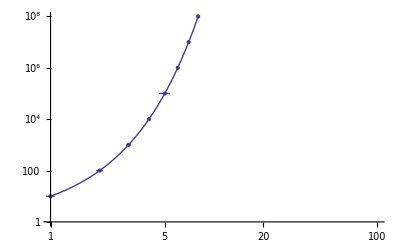

```mathematica
Show[{LogLogPlot[10^x,{x,1,10},PlotRange->{{10^0,10^2},{10^0,10^8}}],lerrorplot}]
```